```mathematica
ClearAll["Global`*"]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/data.csv"][[2;;]];
t=Table[{t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

{{2,0.73452},{3,0.734492},{4,0.73445},{5,0.734393},{6,0.734323},{7,0.734238},{8,0.73414},{9,0.734027},{10,0.7339},{11,0.73376},{12,0.733605},{13,0.733436},{14,0.733253},{15,0.733056},{16,0.732845},{17,0.73262},{18,0.732381},{19,0.732128},{20,0.731861},{21,0.73158},{22,0.731285},{23,0.730977},{24,0.730654},{25,0.730318},{26,0.729967},{27,0.729603},{28,0.729225},{29,0.728833},{30,0.728428},{31,0.728008},{32,0.727575},{33,0.727129},{34,0.726668},{35,0.726194},{36,0.725706},{37,0.725205},{38,0.72469},{39,0.724162},{40,0.72362},{41,0.723065},{42,0.722497},{43,0.721915},{44,0.721319},{45,0.720711},{46,0.720089},{47,0.719454},{48,0.718806},{49,0.718145},{50,0.717472},{51,0.716785},{52,0.716085},{53,0.715372},{54,0.714647},{55,0.713909},{56,0.713159},{57,0.712396},{58,0.71162},{59,0.710833},{60,0.710033},{61,0.709221},{62,0.708397},{63,0.707561},{64,0.706713},{65,0.705853},{66,0.704982},{67,0.7041},{68,0.703206},{69,0.702301},{70,0.701385},{71,0.700458},{72,0.699521},{73,0.703341},{74,0.703346},{75,0.703349},{76,0.70335},{77,0.70335},{78,0.703349},{79,0.703347},{80,0.703346},{81,0.703345},{82,0.703345},{83,0.703346},{84,0.70335},{85,0.703357},{86,0.703367},{87,0.703382},{88,0.703401},{89,0.703426},{90,0.703458},{91,0.703497},{92,0.703543},{93,0.703599},{94,0.703665},{95,0.703741},{96,0.703829},{97,0.703929},{98,0.704043},{99,0.704172},{100,0.700728},{101,0.696067},{102,0.758648},{103,0.754998},{104,0.751301},{105,0.747557},{106,0.743766},{107,0.739929},{108,0.736044},{109,0.732112},{110,0.728132},{111,0.724105},{112,0.720031},{113,0.715909},{114,0.71174},{115,0.707522},{116,0.703257},{117,0.698944},{118,0.765347},{119,0.765517},{120,0.765689},{121,0.765862},{122,0.766037},{123,0.766214},{124,0.766392},{125,0.766572},{126,0.766753},{127,0.766936},{128,0.76712},{129,0.767306},{130,0.767494},{131,0.767683},{132,0.760961},{133,0.752397},{134,0.743769},{135,0.735087},{136,0.726363},{137,0.717606},{138,0.708828},{139,0.700036},{140,0.691241},{141,0.724384},{142,0.725331},{143,0.726259},{144,0.727165},{145,0.728048},{146,0.728907},{147,0.72974},{148,0.727812},{149,0.725045},{150,0.722239},{151,0.719395},{152,0.716513},{153,0.713593},{154,0.710634},{155,0.707638},{156,0.704603},{157,0.701532},{158,0.698422},{159,0.704308},{160,0.704196},{161,0.704062},{162,0.703901},{163,0.70371},{164,0.703484},{165,0.703217},{166,0.702905},{167,0.702544},{168,0.702129},{169,0.701655},{170,0.701118},{171,0.700515},{172,0.699841},{173,0.80392},{174,0.805621},{175,0.807202},{176,0.808657},{177,0.80998},{178,0.811163},{179,0.812199},{180,0.812746},{181,0.811302},{182,0.809846},{183,0.808377},{184,0.806029},{185,0.801916},{186,0.797727},{187,0.793463},{188,0.789121},{189,0.783177},{190,0.773332},{191,0.763189},{192,0.752752},{193,0.742028},{194,0.731024},{195,0.719748},{196,0.708211},{197,0.696424},{198,0.793438},{199,0.784622},{200,0.775701},{201,0.766669},{202,0.757525},{203,0.748263},{204,0.738879},{205,0.729369},{206,0.719728},{207,0.709952},{208,0.700036},{209,0.689978},{210,0.759722},{211,0.759989},{212,0.760207},{213,0.760373},{214,0.760484},{215,0.76054},{216,0.760538},{217,0.760477},{218,0.760357},{219,0.760177},{220,0.759937},{221,0.759638},{222,0.759279},{223,0.758863},{224,0.755524},{225,0.751244},{226,0.746889},{227,0.742461},{228,0.737961},{229,0.733392},{230,0.728756},{231,0.721553},{232,0.713287},{233,0.703623},{234,0.693668},{235,0.70925},{236,0.701408},{237,0.693456},{238,0.643198},{239,0.750141},{240,0.749154},{241,0.748113},{242,0.747017},{243,0.74587},{244,0.74467},{245,0.743419},{246,0.742117},{247,0.740767},{248,0.734152},{249,0.722898},{250,0.711126},{251,0.699115},{252,0.751119},{253,0.740169},{254,0.728995},{255,0.717591},{256,0.705946},{257,0.694056},{258,0.683997},{259,0.677281},{260,0.680178},{261,0.699974},{262,0.750833},{263,0.758986},{264,0.762223},{265,0.7546},{266,0.743116},{267,0.730457},{268,0.71759},{269,0.704509},{270,0.691208},{271,0.801084},{272,0.801757},{273,0.802434},{274,0.803113},{275,0.803795},{276,0.80106},{277,0.794596},{278,0.787981},{279,0.781212},{280,0.774291},{281,0.767217},{282,0.756863},{283,0.74326},{284,0.729293},{285,0.714979},{286,0.700339},{287,0.685394},{288,0.694081},{289,0.698269},{290,0.723372},{291,0.738786},{292,0.75435},{293,0.769877},{294,0.758866},{295,0.744999},{296,0.730779},{297,0.716206},{298,0.701285},{299,0.686022},{300,0.690204},{301,0.711184},{302,0.707066},{303,0.702814},{304,0.698426},{305,0.753093},{306,0.739735},{307,0.726035},{308,0.71198},{309,0.697558},{310,0.636796},{311,0.668987},{312,0.674012},{313,0.756578},{314,0.755849},{315,0.75504},{316,0.743013},{317,0.727266},{318,0.711094},{319,0.694496},{320,0.69661},{321,0.675138},{322,0.813574},{323,0.813341},{324,0.805291},{325,0.796367},{326,0.78725},{327,0.777941},{328,0.768442},{329,0.754104},{330,0.738161},{331,0.721746},{332,0.704884},{333,0.687604},{334,0.61989},{335,0.677357},{336,0.676366},{337,0.667963},{338,0.739995},{339,0.751034},{340,0.734122},{341,0.716685},{342,0.698754},{343,0.654167},{344,0.652991},{345,0.651492},{346,0.649385},{347,0.64788},{348,0.646366},{349,0.644205},{350,0.75153},{351,0.733947},{352,0.715787},{353,0.697061},{354,0.69579},{355,0.694148},{356,0.642193},{357,0.627327},{358,0.6259},{359,0.687128},{360,0.683949},{361,0.624969},{362,0.623401},{363,0.673356},{364,0.660364},{365,0.659242},{366,0.656631},{367,0.652236},{368,0.64984},{369,0.743079},{370,0.74228},{371,0.728258},{372,0.696188},{373,0.736474},{374,0.715027},{375,0.693292},{376,0.738555},{377,0.704303},{378,0.66869},{379,0.467199},{380,0.468029},{381,0.67252},{382,0.66824},{383,0.665472},{384,0.660476},{385,0.610123},{386,0.61822},{387,0.626576},{388,0.635131},{389,0.628079},{390,0.467979},{391,0.467889},{392,0.46792},{393,0.512595},{394,0.512896},{395,0.520792},{396,0.519723},{397,0.520201},{398,0.522087},{399,0.522239},{400,0.588468}}

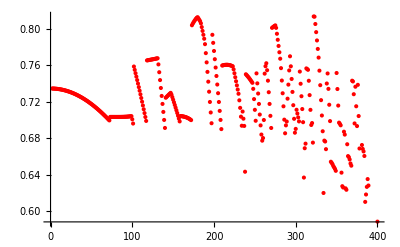

```mathematica
plot1=ListPlot[t,PlotStyle->Red,PlotRange->Automatic]
```